## Neural Network Exercise

##### Kim Mingi (xp2425@khu.ac.kr)

Reference

Wolfram Tutorial “Introduction to Neural Nets”  https://reference.wolfram.com/language/tutorial/NeuralNetworksIntroduction.html#1969481202

MNIST handwriting examples

```mathematica
ResourceSearch["MNIST"]
```

{ResourceObject[…],ResourceObject[…],ResourceObject[…],ResourceObject[…]}

```mathematica
trainingData=ResourceData["MNIST","TrainingData"]
```

{-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,59910,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9}
 |  |  |  |

```mathematica
testData=ResourceData["MNIST","TestData"]
```

{-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,9910,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9}
 |  |  |  |

Pick a few random examples

```mathematica
RandomSample[trainingData,3]
```

{-Graphics-→0,-Graphics-→2,-Graphics-→3}

### 1. Introduction to NN layers

Layers in Mathematica

```mathematica
?*Layer
```

Create a LinearLayer that takes as input a vector of length 2 and produces as output a vector of length 3

```mathematica
linear=LinearLayer[3,"Input"->2]
```

LinearLayer[<>]

```mathematica
linear[{2,3}]
```

$Failed

Above layer is an ‘uninitialized layer’ which is to say, the learning is not yet started. By using NetInitialize, we can initialize the layer

```mathematica
initLinear=NetInitialize[linear]
```

LinearLayer[<>]

```mathematica
initLinear[{{2,3},{2,4},{1,2}}]
```

{{2.38762,1.40096,0.639938},{3.027,1.76667,0.264892},{1.5135,0.883337,0.132446}}

Without pesky calculations, we can easily ‘extract’ the weight and biases.

```mathematica
W=NetExtract[initLinear,"Weights"];
W//MatrixForm
```

(0.234746 | 0.639378
0.151909 | 0.365714
0.882538 | -0.375046)

```mathematica
NetExtract[initLinear,"Biases"]
```

{0.,0.,0.}

```mathematica
Dot[W,{2,3}]
```

{2.38762,1.40096,0.639938}

LinearLayer has only one input, on the other hand, some layers have more than two inputs; MeanSquaredLossLayer needs the input and the target as two inputs

```mathematica
msloss=MeanSquaredLossLayer[]
```

MeanSquaredLossLayer[<>]

Apply the layer to two inputs

```mathematica
msloss[<|"Input"->{1,2,3},"Target"->{4,0,4}|>]
```

4.66667

### 2. Net Encoders & Net Decoders

Before we train or test the data, it should be transformed to numeric tensor, which is a NetEncoder’s job; to translate the data to numeric tensors. Let’s see some of the simple examples

```mathematica
imageenc=NetEncoder[{"Image",{12,12},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

Above encoder produces a 1×12×12 tensor

```mathematica
imageenc[-Graphics-]//MatrixForm
```

((1.
1.
1.
0.992157
1.
1.
1.
1.
0.996078
1.
1.
1.) | (1.
1.
0.996078
1.
0.992157
0.843137
0.737255
0.898039
1.
0.996078
1.
1.) | (1.
0.996078
1.
0.839216
0.266667
0.0156863
0.
0.14902
0.937255
1.
0.996078
1.) | (0.992157
1.
0.878431
0.0470588
0.
0.403922
0.619608
0.
0.752941
1.
0.988235
1.) | (0.996078
1.
0.945098
0.615686
0.694118
0.960784
0.843137
0.00392157
0.694118
1.
0.988235
1.) | (1.
1.
1.
1.
1.
0.976471
0.509804
0.00392157
0.796078
0.996078
0.988235
1.) | (1.
0.996078
0.996078
0.972549
0.494118
0.129412
0.0392157
0.027451
0.905882
1.
0.988235
1.) | (1.
0.992157
0.996078
0.423529
0.
0.00392157
0.
0.
0.364706
0.94902
1.
0.996078) | (0.996078
1.
0.972549
0.121569
0.0392157
0.
0.447059
0.533333
0.
0.14902
0.521569
0.996078) | (1.
0.996078
1.
0.396078
0.121569
0.592157
1.
1.
0.627451
0.
0.211765
1.) | (1.
1.
1.
0.988235
0.972549
1.
0.996078
0.988235
1.
0.764706
0.839216
1.) | (1.
1.
1.
1.
1.
0.988235
1.
1.
0.992157
1.
1.
1.))

Let’s encode some arbitrary images!

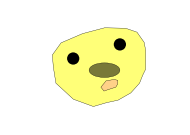

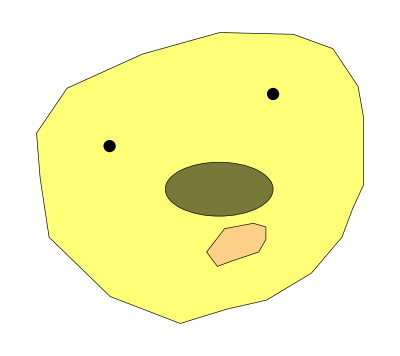
```mathematica
img=-Graphics-;
```

```mathematica
ImageDimensions[img]
```

{360,322}

```mathematica
imageenc[img]//MatrixForm
```

((1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.) | (1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.) | (1.
1.
1.
0.74902
0.25098
0.
0.
0.498039
0.74902
1.
1.
1.) | (1.
1.
0.74902
0.
0.
0.
0.
0.
0.
0.74902
1.
1.) | (1.
0.74902
0.
0.
0.
0.
0.
0.
0.
0.25098
1.
1.) | (1.
0.498039
0.
0.
0.
0.
0.
0.
0.
0.
1.
1.) | (1.
0.
0.
0.
0.
0.
0.
0.
0.
0.
1.
1.) | (1.
0.
0.
0.
0.
0.
0.
0.
0.
0.498039
1.
1.) | (1.
0.25098
0.
0.
0.
0.
0.
0.
0.
0.74902
1.
1.) | (1.
0.74902
0.
0.
0.
0.
0.
0.
0.74902
1.
1.
1.) | (1.
1.
0.74902
0.498039
0.
0.
0.25098
0.74902
1.
1.
1.
1.) | (1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.))

```mathematica
imageenc[img]//Dimensions
```

{1,12,12}

We can attach encoder to a layer

```mathematica
pool=PoolingLayer[10,"Input"->NetEncoder[{"Image",64}]]
```

PoolingLayer[<>]

Then we can directly apply the image the layer

```mathematica
pool[img]//Shallow
```

{{{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},«45»},{{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},«45»},{{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},{«55»},«45»}}

Convert the output back to an image

```mathematica
Image[%,Interleaving->False]
```

-Graphics-

Finally create the final image encoder for MNIST, whose grayscale images are of 28×28.

```mathematica
mnistEnc=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
trainingData[[1,1]]//ImageDimensions
```

{28,28}

Next, create a decoder for MNIST handwritings. Conversely, decoder translate the numeric tensor to some class.  In case of MNIST, there are ten classes, from 0 to 9.

```mathematica
mnistDec=NetDecoder[{"Class",Range[0,9]}]
```

NetDecoder[<>]

```mathematica
mnistDec[{0,0,0,0,0,0,0,0,0,1}]
```

9

```mathematica
mnistDec[{0.1,0.3,0.6,0,0,0,0,0,0,0},"TopProbabilities"]
```

{2→0.6,1→0.3,0→0.1}

```mathematica
mnistDec[{0.1,0.3,0.6,0,0,0,0,0,0,0},"Entropy"]
```

0.897946

Similarly to encoder, we can attach a decoder to the layer

```mathematica
pool=PoolingLayer[10,"Input"->NetEncoder[{"Image",64}],"Output"->NetDecoder["Image"]]
```

PoolingLayer[<>]

```mathematica
pool[img]
```

-Graphics-

Now construct NN to concatenate the layers together.

```mathematica
uninitializedLenet=NetChain[{ConvolutionLayer[20,5],ElementwiseLayer[Ramp],PoolingLayer[2,2],ConvolutionLayer[50,5],ElementwiseLayer[Ramp],PoolingLayer[2,2],FlattenLayer[],LinearLayer[500],ElementwiseLayer[Ramp],LinearLayer[10],SoftmaxLayer[]},"Input"->mnistEnc,"Output"->mnistDec]
```

NetChain[]

Note: Ramp: ReLU

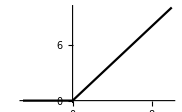

```mathematica
Plot[Ramp[x],{x,-5,10}]
```

```mathematica
lenet=NetInitialize[uninitializedLenet]
```

NetChain[]

```mathematica
samples=RandomSample[trainingData,10]
```

{-Graphics-→0,-Graphics-→6,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→0,-Graphics-→1,-Graphics-→9}

```mathematica
samplelist=Table[samples[[i,1]],{i,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lenet[samplelist]
```

{8,8,8,7,8,8,8,8,8,8}

Pretty stupid...